# S2S Evaluation

BX Pan
2017.9.12

```mathematica
GraphicsRow[{ImageResize[Import["/Users/lambda/Desktop/tianyuanjushi.jpg"],{300,220}],
            ImageResize[Import["/Users/lambda/Desktop/cyberpunk.jpg"],{300,220}]}]
```

-Graphics-

## Introduction

The importance of s2s prediction for west coast United States

Located near the southern margin of the prevailing Pacific storm track, California receives most of its annual precipitation over the course of a small number of heavy precipitation events during its well-defined
winter rainy season

Dam problem. An earlier  detection of potential extremes

General Problem Definition

There is consistent effort toward bridging the predictability gap between weather forecasts(from hourly to 2 weeks) and climate predictions(from 3 to 6 months)\cite[]. The physical difficulty of the intermediate problem have been stressed since people began to calculate the weather\cite[], and well illustrated in reviews of following attempts\cite[].  Improvements in observation, computing and physical understandings 
gain the medium-range forecasting with higher spatial resolution and extended forecasting period. 
, together with the coupling of low frequent evolving ocean and land processes, have extended medium-range forecasting by

Improve of observation

Improve of

Increase resolution. Tibaldi 1988

Couple ocean with atmosphere.

Ensemble

Since the 1980s, medium-range forecasting has made considerable progress, with about 2 days of predictability gained in the last 20 yr, because of improvements in the model physics and improvements in the generation of initial conditions. (Vitart, Monthly Forecasting at ECMWF)

Meanwhile, demand for accessibility/ tailored for use are increasing, especially climate change and frequent hydremeteorological extremes. (advice. how to use?) .  stress precipitation.

Thehierarchicalmodelingapproachallowsoneto   give proper weight to the understanding provided by the   models vs. their realism: back-and-forth between    “toy” (conceptual) and detailed (“realistic”) models,    and between models and data.

The monthly forecasts are based on an ensemble of 51 coupled ocean–atmosphere integrations (one control and 50 perturbed forecasts)

The 50 perturbations are produced using the singular vector method (Buizza and Palmer 1995).

How are improvements achieved?

Ensemble of

The opportunity

A database containing subseasonal to seasonal forecasts from 11 operational centers is
available to the research community and will help advance our understanding of predictability
at the subseasonal to seasonal time range.

They focus on globe. However, here we only focus on a maybe most difficult place, west coast united states. 
Why it is difficult and why it is important?

Specify the question

Ensemble of

Related Works

S2S Atmospheric River

What did it do

What’s its limitation

S2S Monsoon

Target of this research

Assess and Diagnose the ability to s2s QPF, offer baselines for other attempts, including statistical models.

Search potential forecast windows based on climate background information

assess their ability to simulate the Asian monsoon.

There is consistent effort toward bridging the predictability gap between short range weather forecasts(from hourly to 2 weeks) and long range climate predictions(from 3 to 6 months)\cite[]. The physical difficulty of this intermediate problem have been stressed since the dawn of dynamical weather forecast\cite[], and well illustrated in reviews of every not-so-satisfying attempt.

It is
modeled in part on The Observing System Research
and Predictability Experiment (THORPEX) Interactive Grand Global Ensemble (TIGGE) database for mediumrange
forecasts (up to 15 days; Bougeault et al. 2010)
and the Climate-System Historical Forecast Project
(CHFP; http://wcrp-climate.org/index.php/wgsip-chfp
/chfp-overview) for seasonal forecasts. The research is
organized around a set of six topics (MJO, monsoons,
Africa, extremes, teleconnections, and verification),
each intersected by cross-cutting research and modeling
issues and applications and user needs. The latest science
plans of each subproject are available online (www
.s2sprediction.net/static/documents#reports).

Definition

The initial-value problem → numerical weather prediction (NWP)

easiest

The asymptotic problem →long-term climate

a little harder

The intermediate problem→S2S, low-frequency variability (LFV) , multiple equilibria, long-periodic oscillations, intermittency, slow transients, “tipping points”.

hardest

-- Paraphrasing John von Neumann

Motivation besides pure scientific inquiry

Demands are growing rapidly in the operational prediction and applications communities for forecasts that fill the gap between medium-range weather (up to 15 days) and long-range or seasonal (3–6 months) forecasts. But why?
Forecasting for this time range has so far received much less attention than medium range and multiseason prediction despite the considerable socioeconomic value that could be derived from such forecasts.

changes in risks of extreme events or opportunities for optimizing resource management decisions. How to quantify?

what else

Many challenges remain to make subseasonal forecasts sufficiently reliable, skillful, and tailored for users, a great return on investment in weather and climate science and model development is to be expected if the science and forecast products of subseasonal to seasonal prediction can be successfully connected to societal applications.

## Data

S2S Database

CPC Precipitation

## Verification Scores

Deterministic Scores

Probabilistic Scores

ROC Score

Brier Skill

## Linear Inverse Model? What the ghost?

## Detecting the Forecast Window

## Demo

```mathematica
SetDirectory["/Users/lambda/Documents/Data/S2S"];
FileNames[]
```

{BoM,CMA ,.DS_Store,ECCC,ECMWF,HCMR,ISAC-CNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
lat=Import["/Users/lambda/Documents/Data/S2S/BoM/BoM_1981-01-01.nc",{"Datasets","latitude"}];
lon=Import["/Users/lambda/Documents/Data/S2S/BoM/BoM_1981-01-01.nc",{"Datasets","longitude"}];
```

```mathematica
bom1=Import["/Users/lambda/Documents/Data/S2S/BoM/BoM_1982-01-01.nc",{"Datasets","tp"}];
```

```mathematica
Dimensions[bom1]
bom1=Table[bom1[[i+1,;;,;;,;;]]-bom1[[i,;;,;;,;;]],{i,Length[bom1]-1}];
```

{62,32,72,144}

```mathematica
Dimensions[bom1]
```

{61,32,72,144}

```mathematica
Dimensions[Map[Mean,bom1[[;;,;;,1,1]]]]
```

{61}

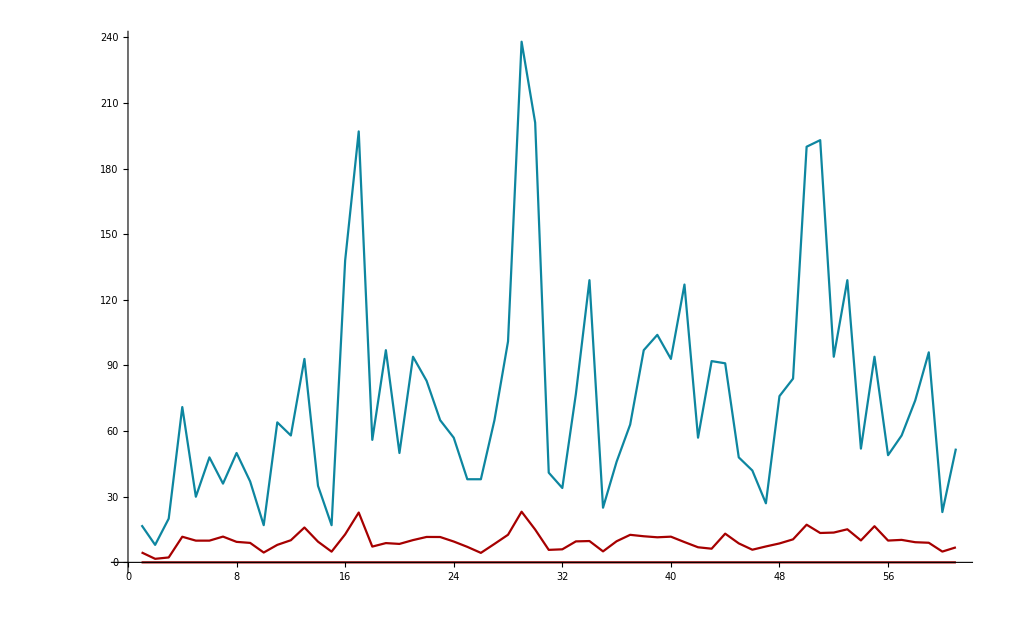

```mathematica
Show[{ListLinePlot[Transpose[Map[MinMax,bom1[[;;,;;,1,1]]]],PlotRange->Full],
ListLinePlot[Map[Mean,bom1[[;;,;;,1,1]]],PlotRange->Full]}]
```

## A strategy

Generate Ensemble GPH field in a certain manner (rather than randomly perturbating but sequentially perturbating)

Use the ensemble GPH field to predict the precipitation distribution.